```mathematica
filePath1 ="/Volumes/D16SD_TD/Study/MSc/results"; fileName1 = { {"imagesBrodatzTexture/textures","t-texmos3.s512","tif"},
		    {"imagesBrodatzTexture/textures","t-1.1.01","tif"},
		    {"imagesBrodatzTexture/textures","t-1.1.07","tif"},
		    {"imagesBrodatzTexture/textures","t-1.5.02","tif"},
		    {"images1","honeycomb2A","tif"},
		    {"images2","lena256b-org","bmp"},
		    {"restmp","honeycomb2_he","tif"}};
picNo = 7;
fileName3 = filePath1<>"/"<>fileName1[[picNo]][[1]]<>"/"<>fileName1[[picNo]][[2]]<>"."<> fileName1[[picNo]][[3]]
image0 = Import[fileName3]
image1 = ColorConvert[image0,"Grayscale"]; 
imgDim = ImageDimensions[image1]
szM = Min[imgDim];
image2 = ImageData[image1, "Byte"];
image2F=Flatten[image2];
min=Min[image2];
max=Max[image2];
```

/Volumes/D16SD_TD/Study/MSc/results/restmp/honeycomb2_he.tif

-Graphics-

{128,128}

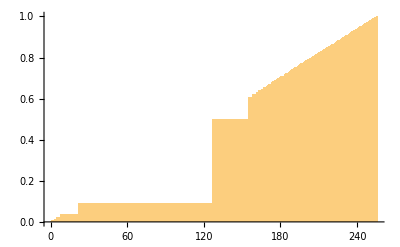

{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256},{0.00219727,0.00457764,0.00799561,0.0139771,0.0139771,0.0211182,0.0211182,0.0211182,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0349121,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.0886841,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.497559,0.606018,0.606018,0.606018,0.619995,0.619995,0.619995,0.629883,0.629883,0.639343,0.639343,0.646118,0.646118,0.654175,0.654175,0.660522,0.665405,0.669983,0.669983,0.676819,0.681885,0.686218,0.68988,0.693542,0.697754,0.701965,0.705994,0.709839,0.709839,0.718201,0.721252,0.723816,0.729553,0.732544,0.738098,0.742126,0.744995,0.749329,0.753906,0.756592,0.760986,0.764587,0.768738,0.772827,0.776672,0.780945,0.784729,0.788208,0.792786,0.795593,0.799072,0.804382,0.806641,0.812439,0.815674,0.81897,0.822632,0.827576,0.830688,0.834106,0.838379,0.843628,0.847107,0.851257,0.854919,0.858826,0.861206,0.865601,0.869873,0.874268,0.878479,0.882813,0.884827,0.889465,0.893921,0.897827,0.901794,0.906006,0.909363,0.913147,0.917175,0.920532,0.925537,0.929626,0.9328,0.937073,0.93988,0.94519,0.949158,0.952759,0.956177,0.960022,0.964783,0.968445,0.972656,0.97644,0.979919,0.984192,0.988037,0.991943,0.996094,1.}}

-Graphics-

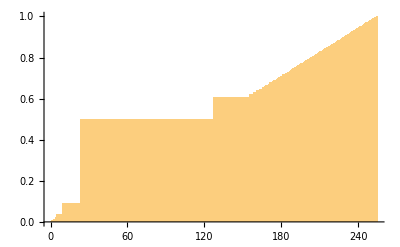

```mathematica
Histogram[image2F,256,"CDF"]
histCount=HistogramList[image2F,256,"Count"]
hist =HistogramList[image2F,256,"CDF"]
intFun = Interpolation[Transpose[{hist[[1]],Join[{0.},hist[[2]]]}]];
image2FEq = ArrayReshape[intFun[image2F],imgDim];
image2O = Image[image2FEq]
image2n = ImageData[image2O, "Byte"];
Histogram[Flatten[image2n],256,"CDF"]
```